```mathematica
projectDir = "/Users/pwrzosek/Documents/GitHub/AvoidedQP/t-J_model";
plotsDir ="./plots/";
dataDir="./data/";
SetDirectory[projectDir];
Off[ToExpression::sntx];
Off[ToExpression::sntxi];
```

```mathematica
(* -------------------------------------------------------------------------------------------------------------------------------- *)
(* Definitions - BEGIN *)
(* -------------------------------------------------------------------------------------------------------------------------------- *)

(* Read Lehmann's representation of the Green's function from a file 'filename' *)
ReadData[filename_]:=(
stream = OpenRead[filename];
n = ToExpression[Read[stream, Word]];
momentum=Table[0.0,n];
energy=Table[{},n];
weight=Table[{},n];
doMomentum=True;
doEnergy=True;
doWeight=True;
in = 1;
While[in≤ n,(
If[doMomentum,(
token=ToExpression[Read[stream, Word]];
While[!NumberQ[token],token=ToExpression[Read[stream, Word]]];
momentum[[in]]=token;
doMomentum=False;
),
If[doEnergy,(
token=ToExpression[Read[stream, Word]];
While[!NumberQ[token],token=ToExpression[Read[stream, Word]]];
While[NumberQ[token],(
AppendTo[energy[[in]],token];
token=ToExpression[Read[stream, Word]];
)];
doEnergy=False;
),
If[doWeight,(
token=ToExpression[Read[stream, Word]];
While[!NumberQ[token],token=ToExpression[Read[stream, Word]]];
While[NumberQ[token],(
AppendTo[weight[[in]],token];
token=ToExpression[Read[stream, Word]];
)];
doWeight=False;
),(
doMomentum=True;
doEnergy=True;
doWeight=True;
in++;
)];
];
];
)];
Close[stream];

{momentum, energy, weight}
);

(* Get exact representation of possible momenta in units of π *)
getMomentumInPi[momentum_]:= Round[momentum*(Length[momentum]-1)/(Pi)]/(Length[momentum]-1);

(* Calculate spectral function A(k,ω) from Lehmann's representation of the Green's function *)
calculate[momentum_,energy_,weight_]:=(
ωMin=Min[energy];
ωMax=Max[energy];
iδ=0.04I;
ωSet=Table[ω, {ω,ωMin-1,ωMax-1,0.01}];
kSet=getMomentumInPi[momentum]*Pi;
spectrum=Table[{kSet[[kDim]],ωSet[[ωDim]],-Im[Total[weight[[kDim]]/(ωSet[[ωDim]]+iδ-energy[[kDim]])]]/Pi},{ωDim,1,Length[ωSet]},{kDim,1,Length[kSet]}];

Flatten[spectrum,1]
);

(* -------------------------------------------------------------------------------------------------------------------------------- *)
(* Definitions - END *)
(* -------------------------------------------------------------------------------------------------------------------------------- *)
```

```mathematica
(* -------------------------------------------------------------------------------------------------------------------------------- *)
(* Listing Files - BEGIN *)
(* -------------------------------------------------------------------------------------------------------------------------------- *)

files=FileNames["lehmann_*.txt",dataDir];
TableForm[Transpose[{Table[n,{n,Length[files]}],files}]]

(* -------------------------------------------------------------------------------------------------------------------------------- *)
(* Listing Files - END *)
(* -------------------------------------------------------------------------------------------------------------------------------- *)
```

1 | ./data/lehmann_l=02_t=1.0_J=1.0_m=1.0_.txt
2 | ./data/lehmann_l=04_t=1.0_J=1.0_m=1.0_.txt
3 | ./data/lehmann_l=06_t=1.0_J=0.4_m=0.0_.txt
4 | ./data/lehmann_l=06_t=1.0_J=0.4_m=1.0_.txt
5 | ./data/lehmann_l=06_t=1.0_J=1.0_m=0.0_.txt
6 | ./data/lehmann_l=06_t=1.0_J=1.0_m=1.0_.txt
7 | ./data/lehmann_l=08_t=1.0_J=0.4_m=0.0_.txt
8 | ./data/lehmann_l=08_t=1.0_J=0.4_m=1.0_.txt
9 | ./data/lehmann_l=08_t=1.0_J=1.0_m=0.0_.txt
10 | ./data/lehmann_l=08_t=1.0_J=1.0_m=1.0_.txt
11 | ./data/lehmann_l=10_t=1.0_J=0.4_m=0.0_.txt
12 | ./data/lehmann_l=10_t=1.0_J=0.4_m=1.0_.txt
13 | ./data/lehmann_l=10_t=1.0_J=1.0_m=0.0_.txt
14 | ./data/lehmann_l=10_t=1.0_J=1.0_m=1.0_.txt
15 | ./data/lehmann_l=12_t=1.0_J=0.4_m=0.0_.txt
16 | ./data/lehmann_l=12_t=1.0_J=0.4_m=1.0_.txt
17 | ./data/lehmann_l=12_t=1.0_J=0.625_m=1.0_.txt
18 | ./data/lehmann_l=12_t=1.0_J=1.0_m=0.0_.txt
19 | ./data/lehmann_l=12_t=1.0_J=1.0_m=1.0_.txt
20 | ./data/lehmann_l=14_t=1.0_J=0.4_m=0.0_.txt
21 | ./data/lehmann_l=14_t=1.0_J=0.4_m=0.1_.txt
22 | ./data/lehmann_l=14_t=1.0_J=0.4_m=0.2_.txt
23 | ./data/lehmann_l=14_t=1.0_J=0.4_m=0.3_.txt
24 | ./data/lehmann_l=14_t=1.0_J=0.4_m=0.4_.txt
25 | ./data/lehmann_l=14_t=1.0_J=0.4_m=0.5_.txt
26 | ./data/lehmann_l=14_t=1.0_J=0.4_m=0.6_.txt
27 | ./data/lehmann_l=14_t=1.0_J=0.4_m=0.7_.txt
28 | ./data/lehmann_l=14_t=1.0_J=0.4_m=0.8_.txt
29 | ./data/lehmann_l=14_t=1.0_J=0.4_m=0.9_.txt
30 | ./data/lehmann_l=14_t=1.0_J=0.4_m=1.0_.txt
31 | ./data/lehmann_l=14_t=1.0_J=0.625_m=1.0_.txt
32 | ./data/lehmann_l=14_t=1.0_J=1.0_m=0.0_.txt
33 | ./data/lehmann_l=14_t=1.0_J=1.0_m=0.2_.txt
34 | ./data/lehmann_l=14_t=1.0_J=1.0_m=0.4_.txt
35 | ./data/lehmann_l=14_t=1.0_J=1.0_m=0.6_.txt
36 | ./data/lehmann_l=14_t=1.0_J=1.0_m=0.8_.txt
37 | ./data/lehmann_l=14_t=1.0_J=1.0_m=1.0_.txt
38 | ./data/lehmann_l=16_t=1.0_J=0.4_m=0.0_.txt
39 | ./data/lehmann_l=16_t=1.0_J=0.4_m=1.0_.txt
40 | ./data/lehmann_l=16_t=1.0_J=1.0_m=0.0_.txt
41 | ./data/lehmann_l=16_t=1.0_J=1.0_m=1.0_.txt

```mathematica
(* -------------------------------------------------------------------------------------------------------------------------------- *)
(* Spectral Function - BEGIN *)
(* -------------------------------------------------------------------------------------------------------------------------------- *)
whichFiles={38};
A={};
Do[(
filename=files[[it]];
{momentum,energy,weight}=ReadData[filename];
AppendTo[A,calculate[momentum,energy,weight]];
),{it,whichFiles}]

(* -------------------------------------------------------------------------------------------------------------------------------- *)
(* Spectral Function - END *)
(* -------------------------------------------------------------------------------------------------------------------------------- *)
```

```mathematica
(* -------------------------------------------------------------------------------------------------------------------------------- *)
(* Plot Setup - BEGIN *)
(* -------------------------------------------------------------------------------------------------------------------------------- *)

FrameTicksFontSize=18;
LegendFontSize=14;
colors=ColorData[{"SunsetColors","Reverse"}];
SetOptions[ListDensityPlot,InterpolationOrder->0,AspectRatio->1/GoldenRatio,ImageSize->600,ColorFunction->colors,FrameTicksStyle->Directive[FrameTicksFontSize,Black],FrameTicks-> {Automatic,{getMomentumInPi[momentum]*Pi,Automatic}},PlotLegends->Placed[BarLegend[Automatic,LabelStyle->Directive[LegendFontSize, Black]],Right],FrameLabel-> {Style["k",FrameTicksFontSize,Black],Style["ω",FrameTicksFontSize,Black]},LabelStyle->Directive[FrameTicksFontSize,Black],FrameStyle->Directive[Black,Thick],PlotRange->{{0,Pi},{-0.5,2},{0,1}},ClippingStyle->Black,ScalingFunctions->{Identity,Identity}]

(* -------------------------------------------------------------------------------------------------------------------------------- *)
(* Plot Setup - END *)
(* -------------------------------------------------------------------------------------------------------------------------------- *)
```

{AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→False,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},BoundaryStyle→None,BoxRatios→Automatic,ClippingStyle→GrayLevel[0],ColorFunction→ColorDataFunction[…],ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DataRange→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},FormatType:>TraditionalForm,Frame→True,FrameLabel→{k,ω},FrameStyle→Directive[GrayLevel[0],Thickness[Large]],FrameTicks→{Automatic,{{0,π/8,π/4,(3 π)/8,π/2,(5 π)/8,(3 π)/4,(7 π)/8,π,(9 π)/8,(5 π)/4,(11 π)/8,(3 π)/2,(13 π)/8,(7 π)/4,(15 π)/8,2 π},Automatic}},FrameTicksStyle→Directive[18,GrayLevel[0]],GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→600,ImageSizeRaw→Automatic,InterpolationOrder→0,LabelStyle→Directive[18,GrayLevel[0]],LightingAngle→None,MaxPlotPoints→Automatic,Mesh→None,MeshFunctions→{#1&,#2&},MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLegends→Placed[BarLegend[Automatic,LabelStyle→Directive[14,GrayLevel[0]]],Right],PlotRange→{{0,π},{-0.5,2},{0,1}},PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RegionFunction→(True&),RotateLabel→True,ScalingFunctions→{Identity,Identity},TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{},VertexColors→Automatic}

```mathematica
plots=Table[ListDensityPlot[A[[it]],PlotLabel->StringJoin[Characters[files[[whichFiles[[it]]]]][[16;;-6]]]],{it,1,Length[A]}];
TableForm[plots]
```

-Graphics-

```mathematica
Do[(
Export[StringJoin[plotsDir,StringJoin[Characters[files[[whichFiles[[it]]]]][[16;;-5]]],".png"],plots[[it]],ImageResolution->200];
),{it,1,Length[plots]}]
```

```mathematica
sliceA=Table[Table[Select[A[[it]],#[[1]]==k&][[;;,2;;3]],{k,{0,Pi/2,Pi}}],{it,Length[whichFiles]}];
```

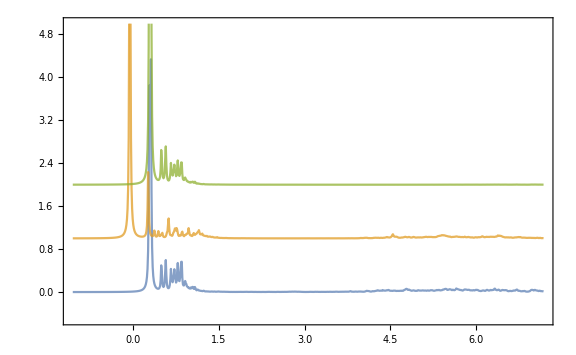

```mathematica
Table[ListLinePlot[Table[sliceA[[it,ik]]+Table[{0,(ik-1)},Length[sliceA[[it,ik]]]],{ik,{1,2,3}}],PlotRange->{All,{-0.5,5}},Frame->True,Axes->False,ImageSize->Large,PlotStyle->Opacity[0.75]],{it,Length[whichFiles]}]//TableForm
```

```mathematica
(* -------------------------------------------------------------------------------------------------------------------------------- *)
(* Finite Size Scaling - BEGIN *)
(* -------------------------------------------------------------------------------------------------------------------------------- *)
whichFiles=Flatten[{
Pick[files,StringMatchQ[files,"*_J=1.0_m=0.0*"]],
Pick[files,StringMatchQ[files,"*_J=1.0_m=1.0*"]]
}];
z={};
Do[(
filename=matchingFile;
{momentum,energy,weight}=ReadData[filename];
AppendTo[z,weight[[1,1]]];
),{matchingFile,whichFiles}]

(* -------------------------------------------------------------------------------------------------------------------------------- *)
(* Finite Size Scaling - END *)
(* -------------------------------------------------------------------------------------------------------------------------------- *)
```

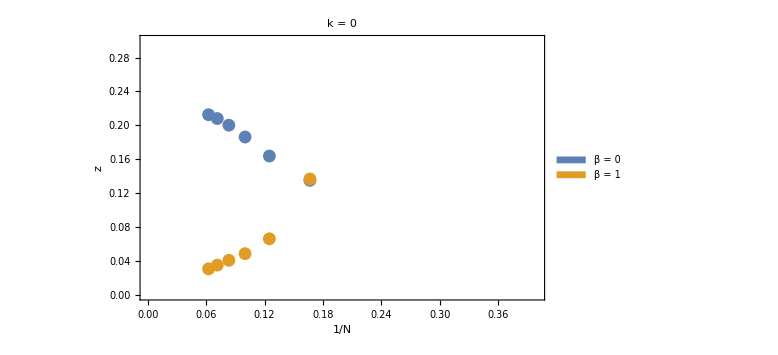

```mathematica
ListPlot[{Table[{1/(2*it +4),z[[it]]},{it,1,6}],Table[{1/(2*it +4),z[[6+it]]},{it,1,6}]},PlotRange->{{0,0.4},{0,0.3}},Frame->True,Axes->False,ImageSize->Large,PlotLegends->SwatchLegend[{Style["β = 0",16],Style["β = 1",16]}],PlotStyle->PointSize[0.016],FrameLabel->{"1/N","z"},LabelStyle->Directive[Black,16],PlotLabel->Style["k = 0", 18]]
```

```mathematica
line = Fit[Table[{l[[it]],z[[8+it]]},{it,1,4}], {1,x,x^2},x]
```

-0.001293301660186+0.533768278746738 x-0.34334905115977 x^2

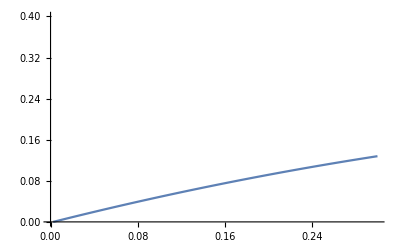

```mathematica
Plot[line,{x,0,0.3},PlotRange->{0,0.4}]
```

```mathematica
z[[9;;]]
```

{0.0486534826741404081,0.0407881289087424076,0.0351014912822687278,0.0307171842839914812}

```mathematica
l=Table[1/(2x+8),{x,1,4}]
```

{1/10,1/12,1/14,1/16}

```mathematica
Factorial[18]/(Factorial[9]*Factorial[9])
```

48620

```mathematica
scbaDirs = {
"./scba/SCBA_J=0.4t_16sites_with_without_2_sublattices/",
"./scba/SCBA_J=1.0t_16sites_with_without_2_sublattices"
};
```

```mathematica
files=FileNames["spec_*B.txt",scbaDirs];
TableForm[Transpose[{Table[n,{n,Length[files]}],files}]]
```

1 | ./scba/SCBA_J=0.4t_16sites_with_without_2_sublattices/spec_0B.txt
2 | ./scba/SCBA_J=0.4t_16sites_with_without_2_sublattices/spec_hpB.txt
3 | ./scba/SCBA_J=0.4t_16sites_with_without_2_sublattices/spec_pB.txt
4 | ./scba/SCBA_J=1.0t_16sites_with_without_2_sublattices/spec_0B.txt
5 | ./scba/SCBA_J=1.0t_16sites_with_without_2_sublattices/spec_hpB.txt
6 | ./scba/SCBA_J=1.0t_16sites_with_without_2_sublattices/spec_pB.txt

```mathematica
specA=Table[Import[f,"Table"],{f,files}]
```

{{{-3.48125,0.00250432},{-3.4625,0.00253183},{-3.44375,0.0025598},{-3.425,0.00263893},{-3.40625,0.00266892},{-3.3875,0.00276781},{-3.36875,0.00280045},{-3.35,0.00283357},{-3.33125,0.00286788},702,{9.85,0.000332632},{9.86875,0.000331323},{9.8875,0.000330021},{9.90625,0.000328726},{9.925,0.00032744},{9.94375,0.000326161},{9.9625,0.000324889},{9.98125,0.000323626},{10.,0.000322369}},5}
 |  |  |  |

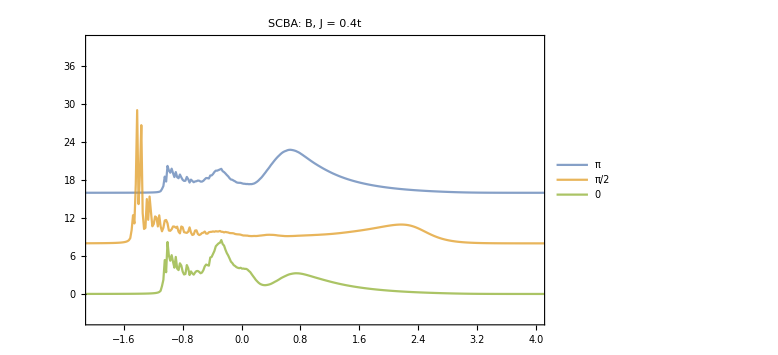

```mathematica
pltSCBA=ListLinePlot[Table[specA[[ik]]+Table[{0,8(ik-1)},Length[specA[[ik]]]],{ik,{3,2,1}}],PlotRange->{{-2,4},{-4,40}},Frame->True,Axes->False,ImageSize->Large,PlotStyle->Opacity[0.75],PlotLegends->{Pi,Pi/2,0,Pi,Pi/2,0},PlotLabel->"SCBA: B, J = 0.4t"]
```

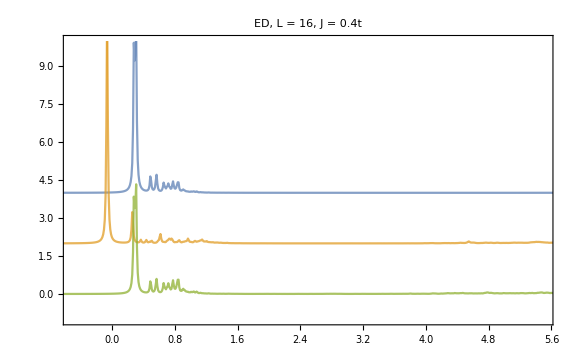
-Graphics-
-Graphics-

```mathematica
pltSCBAvsED=Table[ListLinePlot[Table[sliceA[[it,ik]]+Table[{0,2(ik-1)},Length[sliceA[[it,ik]]]],{ik,{3,2,1}}],PlotRange->{{-0.5,5.5},{-1,10}},Frame->True,Axes->False,ImageSize->Large,PlotStyle->Opacity[0.75],PlotLabel->"ED, L = 16, J = 0.4t"],{it,Length[whichFiles]}];
AppendTo[pltSCBAvsED,pltSCBA]//TableForm
```

```mathematica
Export[StringJoin[plotsDir,"SCBAvsED_noMag.png"],Grid[{pltSCBAvsED}]]
```

./plots/SCBAvsED_noMag.png

```mathematica
Export[StringJoin[plotsDir,"SCBA-B-QP.png"],pltSCBA]
```

./plots/SCBA-B-QP.png

```mathematica
pnDir="./pn/"
```

./pn/

```mathematica
files=FileNames["Pn_*.txt",pnDir];
TableForm[Transpose[{Table[n,{n,Length[files]}],files}]]
```

1 | ./pn/Pn_L=14_J=0.4_m=0.0.txt
2 | ./pn/Pn_L=14_J=0.4_m=1.0.txt

```mathematica
pnDataStructure=Table[(data=Import[file,"Table"];Table[{line-1,data[[line,1]]},{line,Length[data]}]),{file,files}]
```

{{{0,0.123781},{1,0.541034},{2,0.161231},{3,0.0333256},{4,0.0364133},{5,0.0188753},{6,0.0457519},{7,0.0395881}},{{0,0.0702892},{1,0.242338},{2,0.0750125},{3,0.165606},{4,0.0420219},{5,0.119254},{6,0.142217},{7,0.143262}}}

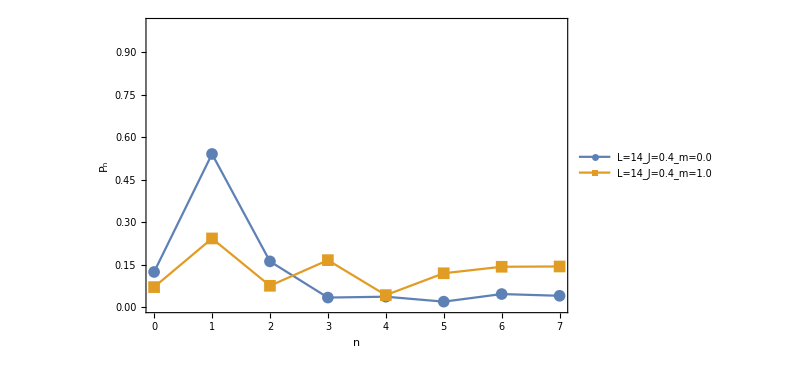

```mathematica
pnPlots=ListPlot[pnDataStructure,Joined->True,PlotMarkers->{Automatic,12},Frame->True,Axes->False,ImageSize->600,FrameStyle->Directive[Black,18],PlotRange->{0,1},PlotLegends->Placed[StringTake[files,{9,24}],Above],FrameLabel->{"n","P_n"}]
```

```mathematica
Export[StringJoin[pnDir,"Pn.png"],pnPlots,ImageResolution->300]
```

./pn/Pn.png